# ECUACIONES DIFERENCIALES

## ESPACIO FASE:

Dr. Jorge Chávez Carlos

Es posible graficar un campo vectorial usando el comando:

VectorPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}]

Es de interes en un sistema de ecuaciones diferenciales graficar el espacio fase, con el sistema de ecuaciones dado como:

x'=ax+by
y'=cx+dy

Por lo tanto para graficar el espacio fase del sistema de ecuaciones se escribe:

VectorPlot[{a x+b y,c x+ d y},{x,x_min,x_max},{y,y_min,y_max}]

## Ejemplo 1:

Introduce el valor de los valores  “a, b, c, d” una vez introducidos

```mathematica
a=.40;
b=1;
c=0;
d=.4;
```

una vez introducidos ejecuta la siguiente linea :

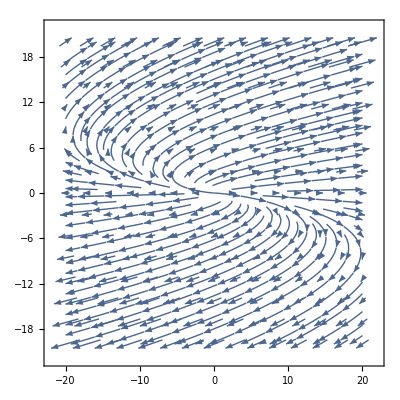

```mathematica
VectorPlot[{a x+b y,c x+d y},{x,-20,20},{y,-20,20},StreamPoints-> Fine,Axes->True]
```

## Ejemplo 2:

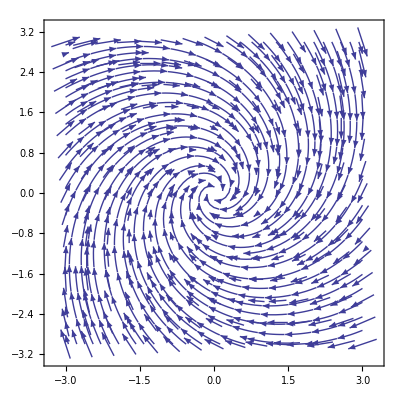

```mathematica
VectorPlot[{-.5x+y,-x-.5y},{x,-3,3},{y,-3,3},StreamPoints-> Fine]
```